```mathematica
Manipulate[
tick;
If[ bInitialized == False,bInitialized = True,] ;
Dynamic@Switch[ tabNumber
,tab1,Plot[x^2,{x,0,1}]
,tab2,Plot[1-x^2,{x,0,1}]
,_,Plot[Sin[x]E^(-x),{x,0,1}] 
]
,Dynamic@TabView[
{
{tab1,"1" ->  Column[ { If[ bInitialized, tabNumber = tab1,] ;Row[{ "1 selected"}] } ] },
{tab2,"2" ->  Column[ { If[ bInitialized, (tabNumber = tab2 ;Beep[]),]  ;Row[{ "2 selected"}] } ] },
{tab3,"3" ->  Column[ { If[ bInitialized, (tabNumber = tab3 ;Beep[]),]   ;Row[{ "3 selected"}] } ] }
}, Dynamic @tabNumber
] 
,{{tick,False},None}
,{{tabNumber,1},None}
,{{tab1, 1}, None}
,{{tab2, 2}, None}
,{{bInitialized, False}, None}
,{{tab3, 3}, None}
,TrackedSymbols:>{tick}
,ControlPlacement->Left
]
```

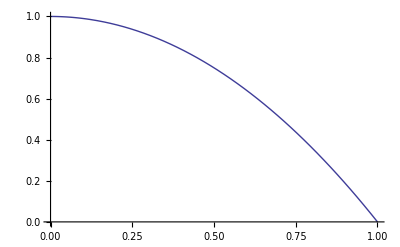

```mathematica
Switch[ 2
,1,Plot[x^2,{x,0,1}]
,2,Plot[1-x^2,{x,0,1}]
,_,Plot[E^x,{x,0,1}] 
]
```

```mathematica
Manipulate[TabView[{{"patt","Pattern"->type},{"motif","Motif"->Grid[{{Column[{Button["Line",type=Line,ImageSize->100],Button["Bezier",type=BezierCurve,ImageSize->100],Button["Point",type=Point,ImageSize->100]}],Graphics[type[{{0,0},{1,0},{0,1}}]]}}]}},Dynamic[choice]],{{type,Line},None},{{choice,"patt"},None}]
```

```mathematica
Manipulate[tick;
Dynamic@Switch[
tabNumber
,tab1,Plot[x^2,{x,0,1}]
,tab2,Plot[1-x^2,{x,0,1}]
,_,Plot[Sin[x] E^(-x),{x,0,1}
]
]
,TabView[{"1"->Column[tabNumber=tab1;{Row[{"1 selected"}]}],"2"->Column[tabNumber=tab2;{Row[{"2 selected"}]}],"3"->Column[tabNumber=tab3;{Row[{"3 selected"}]}]},Dynamic@tabNumber]
,{{tick,False},None},{{tabNumber,1},None},{{tab1,1},None},{{tab2,2},None},{{tab3,3},None},TrackedSymbols:>{tick},ControlPlacement->Left]
```